```mathematica
(* https://math.stackexchange.com/questions/464943/parametric-equations-of-an-oblique-circular-cone *)
```

```mathematica
(* Oblique cones surface area: 
http://mathforum.org/library/drmath/view/55017.html
*)
```

```mathematica
BaseCircle:={r Cos[t], r Sin[t], 0}
```

```mathematica
Vertex:={0, d, h}
```

```mathematica
(1-ν)BaseCircle + ν Vertex
```

{r (1-ν) Cos[t],d ν+r (1-ν) Sin[t],h ν}

```mathematica
ConeAreaIntegral[r_, h_, d_]:=NIntegrate[(r √((r-d Sin[t])^2+h^2))/2,{t, 0, 2Pi}]
```

```mathematica
Integrate[(r √((r-d Sin[t])^2+h^2))/2/.d->0,{t, 0, 2Pi}]
```

π r √(h^2+r^2)

```mathematica
Solve[ r √(h^2+r^2)==rs^2, r]//FullSimplify
```

{{r→-(√(-h^2-√(h^4+4 rs^4)))/(√2)},{r→(√(-h^2-√(h^4+4 rs^4)))/(√2)},{r→-(√(-h^2+√(h^4+4 rs^4)))/(√2)},{r→(√(-h^2+√(h^4+4 rs^4)))/(√2)}}

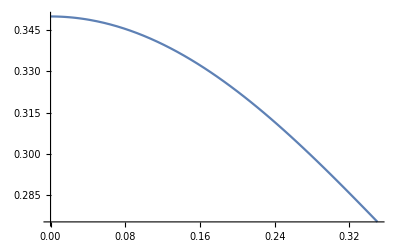

```mathematica
Plot[(√(-h^2+√(h^4+4 rs^4)))/(√2)/.rs->0.35,{h, 0, 0.35}]
```

```mathematica
ConeAreaIntegral[4, 1, 0]
```

51.8125

```mathematica
radiusWithIndentation[radiusWithoutIndentation_, indentationDepth_, offsetFromCenter_]:=r/.FindRoot[ConeAreaIntegral[r, indentationDepth, offsetFromCenter]-Pi radiusWithoutIndentation^2,{r, radiusWithoutIndentation}]//Quiet
```

```mathematica
Table[radiusWithIndentation[0.4, h, 0],{h, 0, 0.4, 0.1}]
```

{0.4,0.3938,0.375826,0.348149,0.314461}

```mathematica
norm[u_]:=√(u.u)

pt1:={0,((offsetFromCenter+radiusCurrent) (indentationDepth^2+(offsetFromCenter+radiusCurrent)^2-√((indentationDepth^2+(offsetFromCenter-radiusCurrent)^2) (indentationDepth^2+(offsetFromCenter+radiusCurrent)^2))))/(2 (indentationDepth^2+(offsetFromCenter+radiusCurrent)^2)),-((indentationDepth (indentationDepth^2+(offsetFromCenter+radiusCurrent)^2-√((indentationDepth^2+offsetFromCenter^2)^2+2 (indentationDepth-offsetFromCenter) (indentationDepth+offsetFromCenter) radiusCurrent^2+radiusCurrent^4)))/(2 (indentationDepth^2+(offsetFromCenter+radiusCurrent)^2)))}

pt2:={0,radiusCurrent,0}


radiusUpperBound:=norm[pt2-pt1]
immersedConeHeight:=norm[{0,offsetFromCenter,-indentationDepth}-pt1]
```

```mathematica
GiveImmersedVolume[currentOffset_]:=Module[{},
radiusInitial=0.42;
indentationDepth=0.1;
(*offsetFromCenter=0.1radiusInitial;*)
offsetFromCenter=currentOffset;
radiusCurrent=radiusWithIndentation[radiusInitial,indentationDepth, offsetFromCenter];
Pi radiusUpperBound^2 immersedConeHeight/3
]
```

```mathematica
offsetValues=Join[{10^-6//N},Table[offset,{offset,0, 0.42, 0.01}][[2;;-1]]];
list=Table[{currentOffset,GiveImmersedVolume[currentOffset]},{currentOffset,offsetValues}];
```

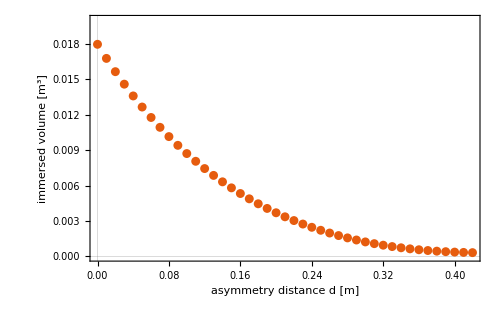

```mathematica
ListPlot[list, PlotTheme->"Scientific", PlotRange->{All,{0, 0.02}}, FrameStyle->Black, ImageSize->500, BaseStyle->20, FrameLabel->{"asymmetry distance d [m]","immersed volume  [m^3]"}]
```

```mathematica
GiveImmersedPlot[currentOffset_]:=Module[{},

radiusInitial=0.42;
indentationDepth=0.1;
(*offsetFromCenter=0.1radiusInitial;*)
offsetFromCenter=currentOffset;
radiusCurrent=radiusWithIndentation[radiusInitial,indentationDepth, offsetFromCenter];

HP=Graphics3D[{Lighter@Blue, Opacity[0.5],Cuboid[pmin,pmax]}];
HP=Graphics3D[{Lighter@Blue, Opacity[0.5],InfinitePlane[{pt1, pt2,pt1+ {1, 0, 0}}]}];

PPIndented=ParametricPlot3D[{radiusCurrent (1-ν) Cos[t],offsetFromCenter ν+radiusCurrent (1-ν) Sin[t],-indentationDepth ν},{t,0,2 Pi},{ν,0,1}, PlotStyle->Directive[Green, Opacity[0.7]],PlotRange->{radiusInitial{-1,1},radiusInitial{-1,1},radiusInitial{-1,1}}, AxesLabel->{x,y, z}, PlotTheme->"Scientific", BaseStyle->20, AxesStyle->Black, ImageSize->500, BoxRatios->{1, 1, 1},  Boxed->False, Axes->False, PlotLabel->"Volume = "<>ToString[Pi radiusUpperBound^2 immersedConeHeight/3]] ;
SphereCenter=Graphics3D[{Red,  Sphere[{0,0,0},0.01]}];
e2=pt1-pt2;
e2=e2/norm[e2]; 

e3=pt1-{0,offsetFromCenter,-indentationDepth};
e3=e3/norm[e3]; 
pmax=pt1+radiusUpperBound(pt2-pt1)/norm[pt2-pt1]+radiusUpperBound{1, 0, 0};
pmin=pt1-radiusUpperBound(pt2-pt1)/norm[pt2-pt1]-radiusUpperBound{1, 0, 0}-norm[pt1-{0,offsetFromCenter,-indentationDepth}]e3;

SpherePt=Graphics3D[{Blue,  Sphere[pt1,0.01], Sphere[pmax,0.01], Sphere[pmin,0.01]}];
cylOffset=Graphics3D[{Red, Cylinder[{{0,offsetFromCenter,0},{0,offsetFromCenter,-1.1 indentationDepth}},0.005]}];
LinePlot=Graphics3D[{Tube[{pt1,pt2}],Tube[{pt1,{0,offsetFromCenter,-indentationDepth}}]}];

Show[PPIndented,(* SphereCenter, cylOffset, SpherePt,LinePlot *)HP]

]
```

```mathematica
Range[0, 0.4, 0.4/3]
```

{0.,0.133333,0.266667,0.4}

```mathematica
GiveImmersedPlot[#]&/@{10^-6, 0.13, 0.27, 0.35}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Pi 0.35^2
```

0.384845

```mathematica
Pi 0.42^2
```

0.554177